```mathematica
S[R_,u_,v_] := {R Sin[u] Cos[v], R Cos[u]Cos[v],R Sin[v]};
T[R_,r_,u_, v_] := {Cos[u] (R + r Cos[v]), Sin[u] (R + r Cos[v]), r Sin[v]};
```

```mathematica
(*Exercício 1*)
ParametricPlot3D[S[3,u,v], {u,0,2π},{v,-π/2,π/2}]
ParametricPlot3D[T[3,1,u,v], {u,0,2π},{v,0,2π}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Exercício 2:*)
(*Se R for negativo, é parametrizada uma esfera com raio |R|.*)
ParametricPlot3D[{S[-3,u,v],S[3,u,v]}, {u,0,π},{v,-π/2,π/2}]
```

-Graphics3D-

```mathematica
(*Exercício 3:*)
(*Se r=0, obtemos apenas um aro circular*)
ParametricPlot3D[T[3,0,u,v], {u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
(*Se 0<R<r, obtemos um toro "gordo", sem buraco no centro e com autointerseções*)
ParametricPlot3D[T[3,4,u,v], {u,0,1.5π},{v,0,2π}]
```

-Graphics3D-

```mathematica
(*Se 0=R<r, obtemos uma esfera.*)
ParametricPlot3D[T[0,4,u,v], {u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
(*Exercício 4*)
(*Esfera: As curvas c/ u fixo (a vermelho) e v fixo (a azul)*)
Show[
ParametricPlot3D[S[1,u,v], {u,0,2π},{v,-π/2,π/2}],
ParametricPlot3D[Table[S[1,u,v],{u,0,3,.5}], {v,-π/2,π/2}, PlotStyle->{Red,Thickness[.02]}],
ParametricPlot3D[Table[S[1,u,v],{v,-1,1,.5}], {u,0,2π}, PlotStyle->{Blue,Thickness[.03]}]
]
```

-Graphics3D-

```mathematica
(*Toro: As curvas c/ u fixo (a vermelho) e v fixo (a azul)*)
Show[
ParametricPlot3D[T[3,1,u,v], {u,0,2π},{v,0,2π}],
ParametricPlot3D[Table[T[3,1,u,v],{u,0,6,.5}], {v,0,2π}, PlotStyle->{Red,Thickness[.02]}],
ParametricPlot3D[Table[T[3,1,u,v],{v,0,6,1}], {u,0,2π}, PlotStyle->{Blue,Thickness[.015]}]
]
```

-Graphics3D-

```mathematica
(*Exercício 5*)
(*Toro: A curva v=u*)
Show[
ParametricPlot3D[T[3,1,u,v], {u,0,2π},{v,0,2π}],
ParametricPlot3D[T[3,1,u,u], {u,0,2π}, PlotStyle->{Red,Thickness[.015]}]
]
```

-Graphics3D-

```mathematica
(*Toro: A mesma curva, sem o toro. Quando vista do ângulo certo, é claro que os pontos não são coplanares, e portanto a figura não pode ser um círculo.*)
Show[
ParametricPlot3D[T[3,1,u,u], {u,0,2π}, PlotStyle->{Red,Thickness[.015]}]
]
```

-Graphics3D-

```mathematica
(*Verificação de que a figura tem pontos que não são coplanares.*)
(*Mais avançado!*)
(*Nas versões mais recentes, seria suficiente usar a função CoplanarPoints*)
p0 = T[3,1,0,0];
deltas = Table[T[3,1,u,u]-p0, {u,{1,2,3}}]; deltas//N//MatrixForm
(*Se os pontos fossem coplanares, os vetores contidos em "deltas" seriam linearmente dependentes, ou seja, a matriz deltas teria rank 1 ou 2, mas verifica-se:*)
MatrixRank[deltas] (*== 3*)
(*Esta resolução não é sujeita a erros de arredondamento porque os números são representados exatamente, mas em caso de dúvida calcula-se o determinante da matriz:*)
Det[N[deltas]] (*Isto é significativamente diferente de zero, portanto a não-independência linear não pode ser atribuida a erros de arredondamento.*)
```

(-2.08717 | 2.97906 | 0.841471
-5.07526 | 2.34949 | 0.909297
-5.98989 | 0.283652 | 0.14112)

3

-3.61496

-Graphics3D-

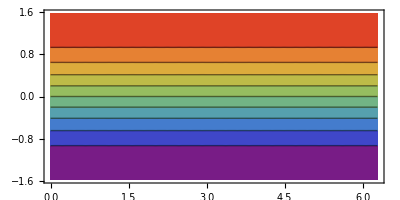

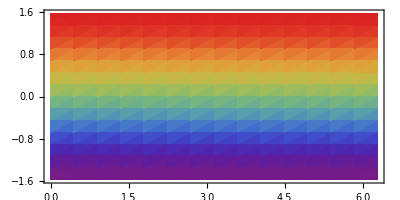

C:\Users\Robly\Desktop\theorems\theorems\ME\spz3d.png

C:\Users\Robly\Desktop\theorems\theorems\ME\spzplane.png

```mathematica
(*Exercício 6*)
spz3d = ParametricPlot3D[S[1,u,v],{u,0,2π},{v,-π/2,π/2}, ColorFunction->Function[{x,y,z,u,v},ColorData["Rainbow"][z]], ViewPoint->{1.3, -2.4, .5}]
spzplane = ContourPlot[S[1,u,v][[3]], {u,0,2π},{v,-π/2,π/2}, AspectRatio->1/2, ColorFunction->"Rainbow"]
DensityPlot[S[1,u,v][[3]], {u,0,2π},{v,-π/2,π/2}, AspectRatio->1/2, ColorFunction->"Rainbow"]
Export[NotebookDirectory[]~StringJoin~"spz3d.png", spz3d]
Export[NotebookDirectory[]~StringJoin~"spzplane.png", spzplane]
```

-Graphics3D-

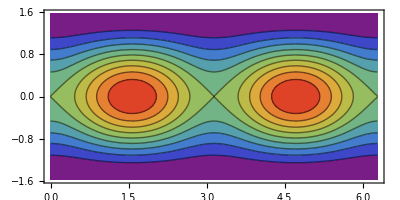

```mathematica
p[x_,y_,z_] := x^2 - z^2
ParametricPlot3D[S[1,u,v],{u,0,2π},{v,-π/2,π/2}, ColorFunction->Function[{x,y,z,u,v},ColorData[{"Rainbow",{-1,1}}][p[x,y,z]]], ColorFunctionScaling->False]
ContourPlot[p@@S[1,u,v], {u,0,2π},{v,-π/2,π/2}, AspectRatio->1/2, ColorFunction->"Rainbow"]
```

-Graphics3D-

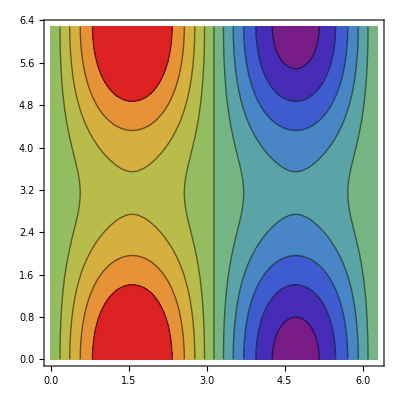

-Graphics3D-

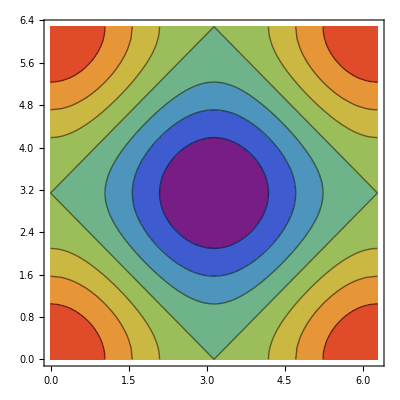

```mathematica
(*Exercício 7*)
h[u_,v_] = Cos[u] + Cos[v];
ParametricPlot3D[T[2,1,u,v],{u,0,2π},{v,0,2π}, ColorFunction->Function[{x,y,z,u,v},ColorData[{"Rainbow",{-3,3}}][y]], ColorFunctionScaling->False]
ContourPlot[T[2,1,u,v][[2]], {u,0,2π},{v,0,2π}, AspectRatio->1, ColorFunction->"Rainbow", Contours->10]
ParametricPlot3D[T[2,1,u,v],{u,0,2π},{v,0,2π}, ColorFunction->Function[{x,y,z,u,v},ColorData[{"Rainbow",{-2,2}}][h[u,v]]], ColorFunctionScaling->False]
ContourPlot[h[u,v], {u,0,2π},{v,0,2π}, AspectRatio->1, ColorFunction->"Rainbow"]
```